# Alteration 2: Bookable well-being meetings

In this model, the Cooked can infect the Human student population, naturally reach threshhold and drop out of Imperial (Removed) and through the use of attending well-being meetings, can re-enter the Human Student population.

-Graphics-

## Non-Dimensionalised Equations

H’[t] == - H[t] C[t] + αC[t]
    	C’[t] == H[t] C[t] - γC C[t] - αC[t]
   	R’[t] == γC C[t]
   	 
Where γC is the Cooked removal rate.

```mathematica
(*Since C is a pre-used term in mathmatica, I've defaulted to Z for now*)

Manipulate[
 Module[
  {
   eqns, sol, H, Z, R, t, Hfunc, Zfunc, Rfunc,
   phasePlotHZ, phasePlotZR, jMatrix, parameterSpace,
   detJ, finalDetJ, traceJ, finalTraceJ
  },
  
  (* System of equations (dimentionless) *)
  eqns = {
    H'[t] == -H[t] Z[t] + α Z[t],
    Z'[t] == H[t] Z[t] - γZ Z[t] - α Z[t],
    R'[t] == γZ Z[t]
  };
  
  (*dacobian*)
  jMatrix = {
    {-Z, -H + α, 0},
    { Z,  H - γZ - α, 0},
    { 0,  γZ, 0}
  };
  
  parameterSpace = 
   ParametricPlot[
    {{d, 0}, {0, t}, {t^2/4, t}},
    {d, -10, 10}, {t, -10, 10},
    PlotRange -> {{-10, 10}, {-10, 10}}
   ];
  
  (* let  NDSolve do all the work *)
  sol = NDSolve[
    {
     eqns,
     H[0] == H0/H0,
     Z[0] == Z0/H0,
     R[0] == R0/H0
    },
    {H, Z, R},
    {t, 0, tmax}
  ];
  
  (* Something something solution functions *)
  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Rfunc = R /. sol[[1]];
  
  traceJ = Tr[jMatrix];
  detJ = Det[jMatrix];
  
  finalTraceJ = 
   traceJ /. {
     H -> (H[tmax] /. sol[[1]]),
     Z -> (Z[tmax] /. sol[[1]]),
     γZ -> γZ,
     α -> α
   };
  
  finalDetJ = 
   detJ /. {
     H -> (H[tmax] /. sol[[1]]),
     Z -> (Z[tmax] /. sol[[1]]),
     γZ -> γZ,
     α -> α
   };
  
  (* Phase Space plotting *)
  phasePlotHZ =
   StreamPlot[
    Evaluate[{
      -H Z + α Z,
      H Z - γZ Z - α Z
    }],
    {H, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    Frame -> True,
    FrameLabel -> {"H (Humans)", "C (Cooked)"}
   ];
  
  phasePlotZR =
   StreamPlot[
    Evaluate[{
      H Z - γZ Z - α Z,
      γZ Z
    } /. {H -> Hfunc[tmax]}],
    {Z, 0, 1}, {R, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    Frame -> True,
    FrameLabel -> {"C (Cooked)", "R (Removed)"}
   ];

    
            (* Make it actually appear on the page *)
  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"Humans (H)", "Cooked (C)", "Removed (R)"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Purple, Thick}},
     Frame -> True,
     FrameLabel -> {"Time (t)", "Population Fractions"}
    ],
    phasePlotHZ,
    phasePlotZR,
    Show[
     parameterSpace,
     ListPlot[{{finalDetJ, finalTraceJ}}, 
      PlotStyle -> PointSize[Large]],
     Frame -> True,
     FrameLabel -> {"Determinant", "Trace"}
    ]
  }]
 ],
 
 (* Sliders for parameters and initial conditions *)
 {{α, 0.5, "Resurrection rate (α)"}, 0, 2, 0.01},
 {{γZ, 0.5, "Cooked removal rate (γ_C)"}, 0, 2, 0.01},
 {{H0, 25000, "Initial humans (H0)"}, 0, 5000, 1},
 {{Z0, 160, "Initial Cooked (C0)"}, 0, 5000, 1},
 {{R0, 0, "Initial removed (R0)"}, 0, 5000, 1},
 {{tmax, 100, "Simulation time"}, 10, 1000000, 1}
]
```

## Eigenvalues + vectors

```mathematica
(* Jacobian matrix *)
  jMatrix = {
    {-Z, -H + α, 0},
    { Z,  H - γZ - α, 0},
    { 0,  γZ, 0}
  };

fixedPoint1 = {Z -> 0};
fixedPoint2 = {H -> 0, Z -> 0};

genEigenVals = Eigenvalues[jMatrix];
genEigenVects = Eigenvectors[jMatrix];
eigenValsP1 = Eigenvalues[jMatrix /. fixedPoint1]
eigenValsP2 = Eigenvalues[jMatrix /. fixedPoint2]
```

{0,0,H-α-γZ}

{0,0,-α-γZ}

```mathematica
{0,0,H-γZ}
```

```mathematica
{-γZ,0,0}
```

## Bifurcation

Check for bifurcation by varying γZ and observing the effect on the final H and Z values.

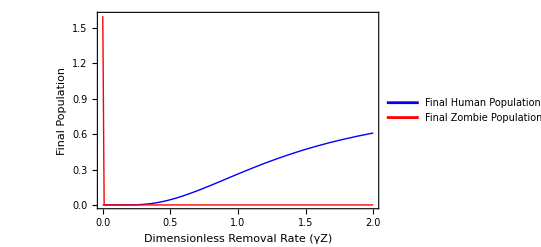

```mathematica
(* Compute final values of H and Z for varying deltaZ *)
finalValues = Table[
  Module[
    {sol, Hfunc, Zfunc, finalH, finalZ},
    (* Define the differential equations *)
    eqns = {
      H'[t] == - H[t] Z[t],
      Z'[t] == H[t] Z[t] - γZ Z[t],
      R'[t] == γZ Z[t]
    };
    
    (* Solve the system numerically for the current deltaZ *)
    sol = NDSolve[
      {eqns, 
       H[0] == 500/500, 
       Z[0] == 300/500,
       R[0] == 0/500
      },
      {H, Z, R}, 
      {t, 0, 10000}
    ];
    
    (* Extract the functions for H and Z *)
    Hfunc = H /. sol[[1]];
    Zfunc = Z /. sol[[1]];
    
    (* Extract the final values of H and Z at time tmax *)
    finalH = Hfunc[10000];
    finalZ = Zfunc[10000];
    
    (* Return the deltaZ and final values for plotting *)
    {γZ, finalH, finalZ}
  ],
  {γZ, 0, 2, 0.01} (* Vary deltaZ from 0 to 2 in steps of 0.01 *)
];

(* Separate deltaZ, H, and Z values for plotting *)
deltaZValues = finalValues[[All, 1]];
finalHValues = finalValues[[All, 2]];
finalZValues = finalValues[[All, 3]];

(* Plot final human and zombie populations as a function of deltaZ *)
ListLinePlot[
  {
   Transpose[{deltaZValues, finalHValues}],
   Transpose[{deltaZValues, finalZValues}]
  },
  PlotRange -> All,
  PlotLegends -> {"Final Human Population (H)", "Final Zombie Population (Z)"},
  PlotStyle -> {{Blue, Thick}, {Red, Thick}},
  AxesLabel -> {"Zombie Removal Rate (γZ)", "Final Population"},
  Frame -> True,
  FrameLabel -> {"Dimensionless Removal Rate (γZ)", "Final Population"}
]
```